```mathematica
input={0.381,0.557,1,1,1,1,1,1,1};(*list of stellar fidelities for the input state*)
target={0.25,0.478,1,1,1};(*list of stellar fidelities for the target state*)
copies=1;(*number of copies of the input state*)
```

```mathematica
nogoregion[input_,target_,copies_]:=RegionUnion[RegionUnion[Flatten[Table[Table[Rectangle[{n*copies/q,0},{1,Max[1-target[[q+1]]-copies(1-input[[n+1]]),0]}],{q,n*copies,Length[target]-1}],{n,1,Length[input]-1}]]],Rectangle[{0,0},{1,Max[1-target[[1]]-copies(1-input[[1]]),0]}]](*computes the no-go region for Gaussian conversion by treating the case n=0 separately. The first coordinate is the success probability and the second coordinate is the error in trace distance*)
```

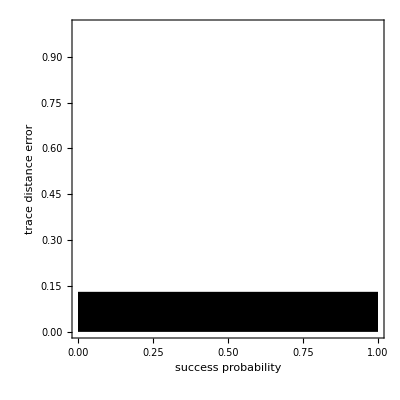

```mathematica
Region[nogoregion[input,target,copies],PlotTheme->"Detailed",PlotRange->{{0,1},{0,1}},FrameLabel->{"success probability","trace distance error"}](*plots the no-go region for Gaussian conversion*)
```